# Best responses

Converts a number n to a list of binary digits. Padded so that the list has length l

```mathematica
toBin[n_,l_]:= Join[ConstantArray[0,l-Length[IntegerDigits[n,2]]],IntegerDigits[n,2]]
```

Calculates the condition for each best response

0 | {0,0,0,0} | {{0→15,True}}
1 | {0,0,0,1} | {{1→14,d+r<1+d s},{1→15,d+r>1+d s}}
2 | {0,0,1,0} | {{2→11,True}}
3 | {0,0,1,1} | {{3→10,True}}
4 | {0,1,0,0} | {{4→13,True}}
5 | {0,1,0,1} | {{5→12,r+d r<1+d s},{5→15,r+d r>1+d s}}
6 | {0,1,1,0} | {{6→9,True}}
7 | {0,1,1,1} | {{7→8,True}}
8 | {1,0,0,0} | {{8→0,d>s+d s},{8→7,d<s+d s}}
9 | {1,0,0,1} | {{9→0,r+s<1&&d>s+d s&&r+d r<1},{9→6,(r+s≤1&&d<s+d s)||(r+s>1&&d+r<1+d s)},{9→9,(r+s<1&&r+d r>1)||(r+s≥1&&d r>s)},{9→15,(-1+r)/(-1+s)<d<s/r&&(2 s>1||r+s>1)}}
10 | {1,0,1,0} | {{10→0,d>s},{10→3,d<s}}
11 | {1,0,1,1} | {{11→0,d>s},{11→2,d<s}}
12 | {1,1,0,0} | {{12→5,True}}
13 | {1,1,0,1} | {{13→4,r+d r<1+d s},{13→15,r+d r>1+d s}}
14 | {1,1,1,0} | {{14→1,True}}
15 | {1,1,1,1} | {{15→0,True}}

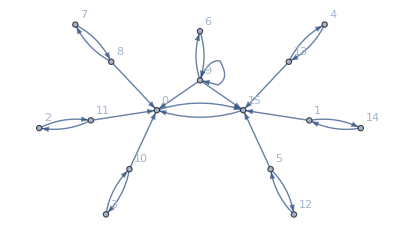

```mathematica
(*The ordering of the game. The first entry has to be a total order*)
ordering = {t>r>s>p};

(*Normalize by setting the outside parameters to 1 and 0.*)
outside = {First[ordering[[1]]/.{Greater ->List}],Last[ordering[[1]]/.{Greater ->List}]};
values = {outside[[1]]==1,outside[[2]]==0};

inside = DeleteCases[ordering[[1]] /.{Greater->List},Alternatives @@ outside];
changes = values/.{Equal->Rule};
restrictions= ordering/.changes;

(*Drawing restrictions*)
drestrictions = Flatten[{restrictions,0<d<1}];

(*All restrictions*)
restrictions = Flatten[{drestrictions,values}];


result[i_, strats_]:=
Module[{input = i, str = strats},
output = {};
transpoints = {};
(*Check every strat to see if it is a best-response*)
Do[{
strat = str[[j]];
(*Get an ordering of the Q-values based on the strategy-pair*)
assumptions = Flatten[{
               If[strat[[1]]==0, Q1000>Q1001, Q1000<Q1001],
               If[strat[[2]]==0, Q1010>Q1011, Q1010<Q1011],
               If[strat[[3]]==0, Q1100>Q1101, Q1100<Q1101],
               If[strat[[4]]==0, Q1110>Q1111, Q1110<Q1111],
               If[input[[1]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[2]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[3]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[4]]==0, Q2110>Q2111, Q2110<Q2111],
               restrictions}];

(*Solve the Bellman equations*)
Assuming[assumptions,
{q1 = Simplify[Boole[Q2000>Q2001] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2000<Q2001] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q2=  Simplify[Boole[Q2000>Q2001] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2000<Q2001] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q3=  Simplify[Boole[Q2100>Q2101] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2100<Q2101] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q4=  Simplify[Boole[Q2100>Q2101] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2100<Q2101] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q5=  Simplify[Boole[Q2010>Q2011] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2010<Q2011] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q6=  Simplify[Boole[Q2010>Q2011] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2010<Q2011] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q7=  Simplify[Boole[Q2110>Q2111] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                         Boole[Q2110<Q2111] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q8=  Simplify[Boole[Q2110>Q2111] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                         Boole[Q2110<Q2111] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])]
}];
sol1=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},{Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];

(*Check when strat is best-response*)
formula = Simplify[Assuming[assumptions,
 Simplify[Reduce[
  If[strat[[1]]==0,Simplify[sol1[[1]][[1]][[2]] > sol1[[1]][[2]][[2]]], Simplify[sol1[[1]][[1]][[2]] < sol1[[1]][[2]][[2]]]] && 
If[strat[[2]]==0,Simplify[sol1[[1]][[3]][[2]] > sol1[[1]][[4]][[2]]], Simplify[sol1[[1]][[3]][[2]] < sol1[[1]][[4]][[2]]]] && 
If[strat[[3]]==0,Simplify[sol1[[1]][[5]][[2]] > sol1[[1]][[6]][[2]]], Simplify[sol1[[1]][[5]][[2]] < sol1[[1]][[6]][[2]]]] && 
If[strat[[4]]==0,Simplify[sol1[[1]][[7]][[2]] > sol1[[1]][[8]][[2]]], Simplify[sol1[[1]][[7]][[2]] < sol1[[1]][[8]][[2]]]],d,Reals]]]];
(*If the strat can be a best-response, add the strategy and the region to the output*)
If[(formula === False)==False , AppendTo[output,{FromDigits[i,2]->j-1,Simplify[formula]}]];
},{j,1,16}];
output
];

(*All binary strategies*)
strats = Table[ Join[ConstantArray[0,4-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]],{i,0,15}];

(*All best-responses*)
transitions = Table[result[strats[[i]],strats],{i,1,16}];

(*Grid of strategies and best-responses*)
grid = Table[{FromDigits[strats[[i]],2], strats[[i]],transitions[[i]]},{i,1,16}];
Grid[grid,Frame->All]

(*Draw a graph with the best-responses*)
edges = Flatten[Table[Table[transitions[[i]][[j]][[1]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}]];
labels = Flatten[Table[Table[transitions[[i]][[j]][[1]] -> transitions[[i]][[j]][[2]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}]];
GraphPlot[edges, VertexLabels->Automatic,  DirectedEdges->True, ImageSize->Full]
```

Find the graphs of the game and their conditions

```mathematica
(*Find the actual possible graphs by adding a restriction on at the time if it does not yield an empty region*)

(*Here will will get all graphs and their regions*)
(*We will initialise with the transitions from 0 and their regions*)
possible = Table[{transitions[[1]][[j]][[1]],transitions[[1]][[j]][[2]]},{j,1,Length[transitions[[1]]]}];

Do[
(*Updated possible after adding the next round of transitions*)
next = {};
Do[
Do[
(*Add a new transition to possible[[k]]*)
function = Assuming[restrictions,FullSimplify[And[possible[[k]][[2]],transitions[[i]][[j]][[2]]]]];
(*If the new region is non empty, add possible[[k]] with the new transition to next*)
If[(function===False)==False,
next = AppendTo[next,{Flatten[{possible[[k]][[1]],transitions[[i]][[j]][[1]]}],Assuming[restrictions,FullSimplify[And[possible[[k]][[2]],function]]]}];
];
,{k,1,Length[possible]}];
,{j,1,Length[transitions[[i]]]}];
possible = next;
,{i,2,16}];        

(*Add the restrictions*)
Graphs = Table[{possible[[i]][[1]],FullSimplify[possible[[i]][[2]]&&( And @@ drestrictions)]},{i,1,Length[possible]}];

(*Delete regions which will now become empty*)
Graphs = DeleteCases[Graphs,{_,False}];

Grid[Table[{i,Graphs[[i]][[1]],Graphs[[i]][[2]]},{i,1,Length[Graphs]}], Frame->All]

edgeslist = Graphs[[All,1]];
todraw = Graphs[[All,2]];
```

1 | {0→15,1→14,2→11,3→10,4→13,5→12,6→9,7→8,8→0,9→0,10→0,11→0,12→5,13→4,14→1,15→0} | d+r<1+d s&&d>s+d s&&r>s>0
2 | {0→15,1→15,2→11,3→10,4→13,5→12,6→9,7→8,8→0,9→0,10→0,11→0,12→5,13→4,14→1,15→0} | r+d r<1&&d+r>1+d s&&s>0&&0<d<1
3 | {0→15,1→14,2→11,3→10,4→13,5→12,6→9,7→8,8→7,9→6,10→0,11→0,12→5,13→4,14→1,15→0} | d<s+d s&&d+r<1+d s&&d>s&&r>s&&0<d<1
4 | {0→15,1→15,2→11,3→10,4→13,5→12,6→9,7→8,8→0,9→9,10→0,11→0,12→5,13→4,14→1,15→0} | r+d r<1+d s&&(r+s≥1||r+d r>1)&&d>s+d s&&d+r>1+d s&&s>0&&0<d<1
5 | {0→15,1→15,2→11,3→10,4→13,5→12,6→9,7→8,8→7,9→9,10→0,11→0,12→5,13→4,14→1,15→0} | d<s+d s&&r+d r<1+d s&&d r>s&&0<d<1
6 | {0→15,1→15,2→11,3→10,4→13,5→12,6→9,7→8,8→7,9→15,10→0,11→0,12→5,13→4,14→1,15→0} | d r<s&&r+d r<1+d s&&1+d s<d+r&&d>s&&0<d<1
7 | {0→15,1→14,2→11,3→10,4→13,5→12,6→9,7→8,8→7,9→6,10→3,11→2,12→5,13→4,14→1,15→0} | d<s&&d+r<1+d s&&1>r>s&&d>0
8 | {0→15,1→15,2→11,3→10,4→13,5→12,6→9,7→8,8→7,9→15,10→3,11→2,12→5,13→4,14→1,15→0} | d<s&&r+d r<1+d s&&1+d s<d+r&&d>0
9 | {0→15,1→15,2→11,3→10,4→13,5→15,6→9,7→8,8→0,9→9,10→0,11→0,12→5,13→15,14→1,15→0} | d>s+d s&&r+d r>1+d s&&1>r>s>0&&d<1
10 | {0→15,1→15,2→11,3→10,4→13,5→15,6→9,7→8,8→7,9→9,10→0,11→0,12→5,13→15,14→1,15→0} | d<s+d s&&d r>s&&r+d r>1+d s&&r<1&&0<d<1
11 | {0→15,1→15,2→11,3→10,4→13,5→15,6→9,7→8,8→7,9→15,10→0,11→0,12→5,13→15,14→1,15→0} | d r<s&&d>s&&r+d r>1+d s&&0<d<1
12 | {0→15,1→15,2→11,3→10,4→13,5→15,6→9,7→8,8→7,9→15,10→3,11→2,12→5,13→15,14→1,15→0} | d<s&&r+d r>1+d s&&1>r>s

Draw the graphs and their regions

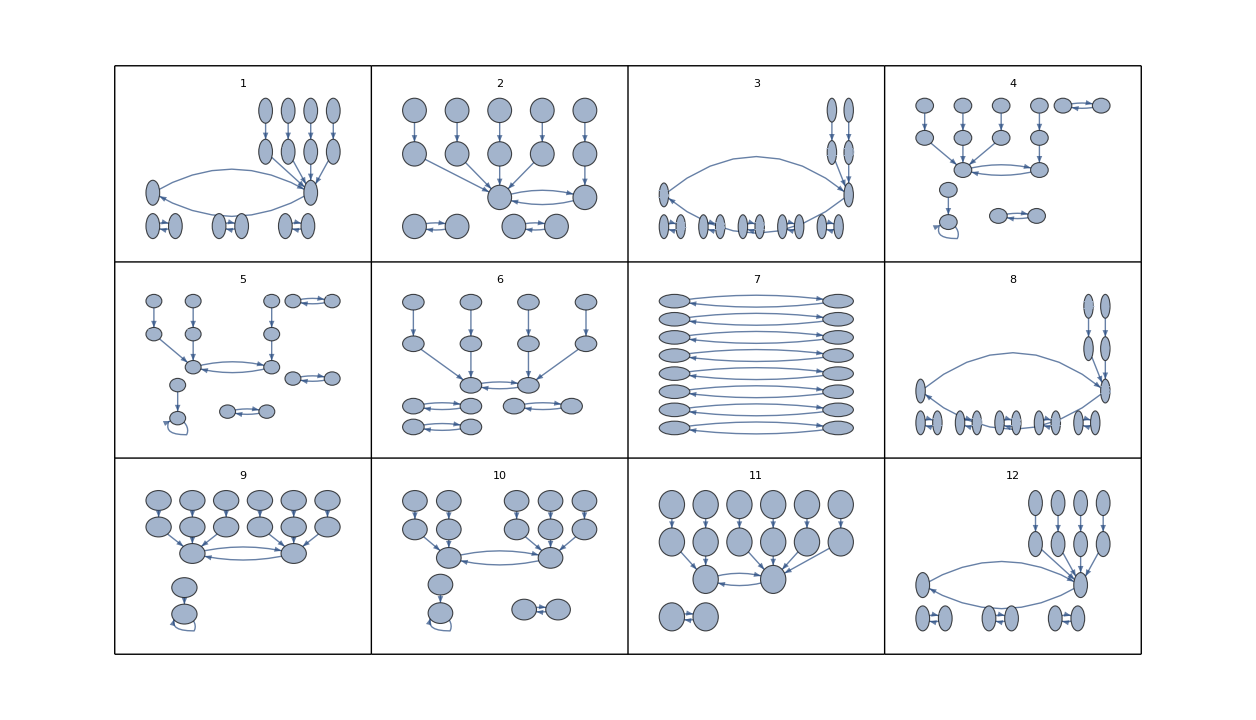

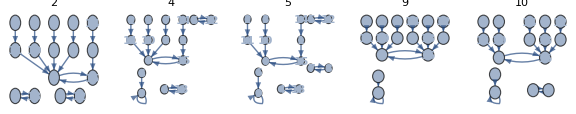

/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/Snow Drift d=0.5.png

```mathematica
(*Make a grid with the different graphs (as square as possible)*)
grid = ArrayReshape[Table[Graphics[GraphPlot[edgeslist[[i]], VertexLabels->Placed[Automatic,Center],VertexSize->.75 , DirectedEdges->True,PlotLabel->i,PlotStyle->Thick, GraphLayout->"LayeredDigraphEmbedding"]],{i,1,Length[edgeslist]}],{Ceiling[Sqrt[Length[Graphs]]],Ceiling[Sqrt[Length[Graphs]]]}];

grid2 ={Table[
Graphics[GraphPlot[edgeslist[[i]], VertexLabels->Placed[Automatic,Center],VertexLabelStyle->Bold,VertexSize->.75 , DirectedEdges->True,PlotLabel->i,PlotStyle->Thick, GraphLayout->"LayeredDigraphEmbedding"]],{i,1,Length[edgeslist]}][[{2,4,5,9,10}]]};

(*Convert the zeroes on the empty spaces in the grid to empty graphics*)
Do[Do[If[grid[[i]][[j]]==0, grid[[i]][[j]] = Graphics[{}]],{j,1,Length[grid[[i]]]}],{i,1,Length[grid]}]

(*Delete the empty rows*)
Do[If[grid[[i]] == ConstantArray[Graphics[{}],Length[grid[[i]]]],grid = grid[[1;;i-1]]; Break[]],{i,1,Length[grid]}]
(*Draw the grid*)
GraphicsGrid[grid,Frame->All,ImageSize->Large]

GraphicsGrid[grid2,Frame->All,ImageSize->Large]

(*Function for drawing the regions of the graphs*)
drawregions[f_,n_]:=
Module[{new = n,formulas= f},
(*Replace the variables by the new values*)
formulas = ReplaceAll[formulas, {d->new,inside[[1]]->x,inside[[2]]->y}];
(*Make the region plot*)
 RegionPlot[formulas,{x,0,1},{y,0,1},AxesLabel->Automatic, PlotStyle->{Pink,Red,Orange,Yellow,Green,Cyan,Blue,Magenta,Purple,Brown,Gray,Black},BoundaryStyle->Black,PlotLegends->Automatic,PerformanceGoal->"Quality",FrameLabel->{inside[[1]],inside[[2]]}]
];

(*Draw the regions for various delta*)
Manipulate[drawregions[todraw,d],{d,0,1}]

(*Get the transition lines*)
test =possible[[All,2]];
test = test /. {And -> List, Or->List,Less -> Equal, LessEqual->Equal,Greater->Equal,GreaterEqual->Equal };
test = DeleteDuplicates[Flatten[test]];

(*Function for drawing the transition lines of the graphs*)
drawLines[f_,n_]:=
Module[{new = n,formulas= f},
formulas = ReplaceAll[formulas, {d->new,inside[[1]]->x,inside[[2]]->y}];
 ContourPlot[Evaluate @(formulas),{x,0,1},{y,0,1},FrameLabel->{inside[[1]],inside[[2]]},BoundaryStyle->{Pink,Red,Orange,Yellow,Green,Cyan,Blue,Magenta,Purple,Brown,Gray,Black},PlotLegends->test]
];

(*Draw the transition lines for various delta*)
Manipulate[drawLines[test,d],{d,0,1}]

Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/Snow Drift d=0.5.png",drawregions[todraw,0.5]]
```

Draw best responses and their regions

```mathematica
(*Get the possible transitions*)
postrans = DeleteDuplicates[Flatten[Graphs[[All,1]]]];

(*Get the graphs where each transition is possible*)
posgraphs = Table[Position[Graphs,postrans[[i]]][[All,1]],{i,1,Length[postrans]}];

(*Get a list of regions where each transition is possible*)
regions = Table[todraw[[posgraphs[[i]]]],{i,1,Length[posgraphs]}];

(*Take the union of each list*)
regions = Table[regions[[i]] /. {List -> Or},{i,1,Length[regions]}];

(*Draw the regions the best responeses (Called volumes as drawregions already existed)*)
drawvolumes[f_,n_,l_]:=
Module[{formulas = f, new = n,legend=l},
formulas = formulas /. {d->new,inside[[1]]->x,inside[[2]]->y};
RegionPlot[formulas,{x,0,1},{y,0,1},FrameLabel->{inside[[1]],inside[[2]]},PerformanceGoal->"Quality",PlotLegends->legend,FrameTicksStyle->15,FrameStyle->15]
];

(*Draw the volumes of the best responses*)
drawvolumes3D[f_,n_,t_]:=
Module[{formulas = f,new=n,type=t},
formulas = formulas /. {List->type,inside[[1]]->x,inside[[2]]->y};
plot1 = RegionPlot3D[formulas,{x,0,1},{y,0,1},{d,0,1},PerformanceGoal->"Quality",PlotStyle->Directive[Specularity[White, 40],Orange],Mesh->None,AxesLabel->Automatic];
plot2 = ContourPlot3D[d==n,{x,0,1},{y,0,1},{d,0,1},ContourStyle->Opacity[0.5],Mesh->None];
Show[plot1,plot2]
];

(*A togglerbar to choose the best responses and whether to draw the union or intersection*)
DynamicModule[{x={},t=And},
{TogglerBar[Dynamic[x],
Table[{regions[[i]],postrans[[i]]} -> postrans[[i]],{i,1,Length[postrans]}],Appearance -> "Vertical" -> {Automatic,15}],
SetterBar[Dynamic[t],{And,Or}],
Manipulate[{drawvolumes[x[[All,1]],d,x[[All,2]]],drawvolumes3D[x[[All,1]],d,t]},{d,0,1}]}
]
```

Get the regions of the fixed points

```mathematica
(*Groups together transitions with the same region*)
grouping[g_]:=
Module[{gr = g},
group = GatherBy[gr,Last];
Do[
graphs = group[[i]][[1]][[3]];
condition = group[[i]][[1]][[2]];transitions =Table[group[[i]][[j]][[1]],{j,1,Length[group[[i]]]}];group[[i]]={transitions,condition,graphs},{i,1,Length[group]}];
group
]

(*All transitions in the big graph*)
trans = Table[{i-1->j-1 },{i,1,256},{j,1,256}];

(*Array to place the conditions and graphs of each transition*)
transitions = ConstantArray[ConstantArray[{},256],256];

(*Find the region for every transition*)
Do[Do[
from = {FromDigits[toBin[trans[[i,j,1,1]],8][[1;;4]],2],FromDigits[toBin[trans[[i,j,1,1]],8][[5;;8]],2]};
to= {FromDigits[toBin[trans[[i,j,1,2]],8][[5;;8]],2],FromDigits[toBin[trans[[i,j,1,2]],8][[1;;4]],2]};
graphs = Intersection[Position[Graphs,from[[1]]->to[[1]]][[All,1]],Position[Graphs,from[[2]]->to[[2]]][[All,1]]];
regions =  Table[todraw[[graphs[[i]]]],{i,1,Length[graphs]}];
AppendTo[transitions[[i]][[j]],{i-1->j-1, regions, graphs}],
{j,1,256}];

(*Delete transitions which are never true*)
transitions[[i]]=DeleteCases[transitions[[i]],{{_Integer->_Integer,{},{}}}],
  {i,1,256}];
transitions = Flatten[transitions,2];

(*Take the union of the regions*)
Do[transitions[[i]][[2]] = FullSimplify[Or @@ transitions[[i]][[2]]],{i,1,Length[transitions]}]

(*Get the fixed points*)
fixed = Cases[transitions,HoldPattern[{a_->a_,_,_}]];

(*Group fixed points with the same region together*)
fixed = grouping[fixed];

(*Plot the fixed points*)
legend = Table["[" <> ToString[fixed[[All,1,1,1]][[i]]] <> "]",{i, Length[fixed[[All,1,1,1]]]}];
DynamicModule[{x={}},
{TogglerBar[Dynamic[x],
Table[{fixed[[i]][[2]],legend[[i]]} -> fixed[[i]][[1]],{i,1,Length[fixed]}],Appearance -> "Vertical" -> {Automatic,4}],
Manipulate[drawvolumes[x[[All,1]],d,x[[All,2]]],{d,0,1}]
}
]
(*Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/Snow Drift d=0.5 3.png",drawvolumes[fixed[[All,2]][[{1,7}]],0.499999999999,legend[[{1,7}]]]]*)
```

```mathematica
markov[graph_] :=
Module[{g=graph},
(*All 256 strategy pairs*)
inputlist = {};
Do[AppendTo[inputlist, Join[ConstantArray[0,8-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,255}];

bestresps = {};
Do[bestresps = AppendTo[bestresps,toBin[g[[i]][[2]],4]],{i,1,Length[g]}];

(*Find the best responses to the pairs*)
counterstrats = {};
Do[
p1 =FromDigits[inputlist[[i]][[1;;4]],2] + 1 ;
p2 = FromDigits[inputlist[[i]][[5;;8]],2] + 1 ;
AppendTo[counterstrats,Join[bestresps[[p2]],bestresps[[p1]]]];
,{i,1,256}];

(*Uniform*)
transitionmatrix = ConstantArray[ConstantArray[0,256],256];
Do[transitionmatrix[[i]][[FromDigits[counterstrats[[i]],2]+1]] = 1,{i,1,256}];

P = DiscreteMarkovProcess[ConstantArray[1/256,256],transitionmatrix]
];

colpercent[index_]:=
Module[{ind=index},
P= markov[edgeslist[[ind]]];
distr= P[256][[2]][[1]];
recclasses = MarkovProcessProperties[P,"RecurrentClasses"];
recstates = Flatten[recclasses];
colclasses = Table[Boole[!MemberQ[Table[MemberQ[collist[[1]],recclasses[[i]][[j]]-1],{j,1,Length[recclasses[[i]]]}],False]],{i,1,Length[recclasses]}];
Total[Table[colclasses[[Position[recclasses,recstates[[i]]][[1]][[1]]]]*distr[[recstates[[i]]]],{i,1,Length[recstates]}]]
];


colpercents = Table[colpercent[i],{i,1,Length[edgeslist]}];
percents = {colpercents, 1-colpercents}
```

{{31/128,33/128,85/256,13/32,101/256,119/256,101/256,119/256,31/64,145/256,141/256,41/64},{97/128,95/128,171/256,19/32,155/256,137/256,155/256,137/256,33/64,111/256,115/256,23/64}}

```mathematica
colarea[0.5,1]
colarea[0.0000001,1]
```

colarea[0.5,1]

colarea[1.×10^-7,1]

1/2

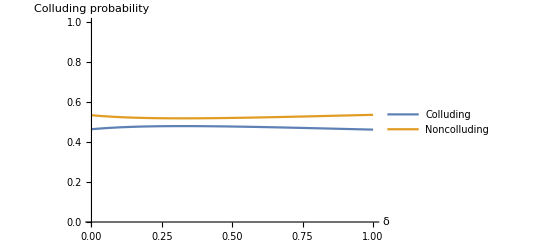

```mathematica
colarea[delta_,type_]:=Sum[percents[[type]][[i]]*Area[ImplicitRegion[todraw[[i]]/.{d->delta,inside[[1]]->x,inside[[2]]->y},{x,y}]],{i,1,Length[todraw]}]
totalarea = colarea[1/2,1]+colarea[1/2,2]
(*Plot[{colarea[x,1]*2,colarea[x,2]*2,colarea[x,3]*2},{x,0,1},PlotLegends->{"Colluding","Semicolluding","Noncolluding"}]*)
plot = Plot[{colarea[d,1]/totalarea,colarea[d,2]/totalarea},{d,0,1},PlotLegends->{"Colluding","Noncolluding"},PlotRange->{0,1},AxesLabel->{"δ","Colluding probability"}]
(*Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/Collusion Snow Drift.png",plot]*)
```

```mathematica
temp = Normalize[percents[[2]] - Min[percents[[2]]],Max]
colors = Table[ColorData["RoseColors"][temp[[i]]],{i,1,Length[percents[[2]]]}]

(*Function for drawing the regions of the graphs*)
drawregions[f_,n_]:=
Module[{new = n,formulas= f},
(*Replace the variables by the new values*)
formulas = ReplaceAll[formulas, {d->new,inside[[1]]->x,inside[[2]]->y}];
(*Make the region plot*)
 RegionPlot[formulas,{x,0,1},{y,0,1},AxesLabel->Automatic, PlotStyle->colors,BoundaryStyle->Black,PlotLegends->Automatic,PerformanceGoal->"Quality",FrameLabel->{inside[[1]],inside[[2]]}]
];

(*Draw the regions for various delta*)
Manipulate[drawregions[todraw,d],{d,0,1}]
```

{1,49/51,79/102,10/17,21/34,15/34,21/34,15/34,20/51,19/102,23/102,0}

{RGBColor[0.697932, 0.135622, 0.111376],RGBColor[0.7085408235294117, 0.1776161176470588, 0.1402526666666667],RGBColor[0.760269568627451, 0.3733237843137255, 0.2743905098039216],RGBColor[0.8092544117647059, 0.5345317647058823, 0.3813475882352941],RGBColor[0.8109315294117647, 0.5181347647058823, 0.37127364705882354],RGBColor[0.7170470588235294, 0.5358538235294118, 0.3710299411764706],RGBColor[0.8109315294117647, 0.5181347647058823, 0.37127364705882354],RGBColor[0.7170470588235294, 0.5358538235294118, 0.3710299411764706],RGBColor[0.6794895490196078, 0.5304035686274511, 0.3625699019607843],RGBColor[0.3753510784313726, 0.3823055980392157, 0.21666061862745098],RGBColor[0.4300262156862745, 0.4067194019607843, 0.24418406862745098],RGBColor[0.151125, 0.307698, 0.0888533]}

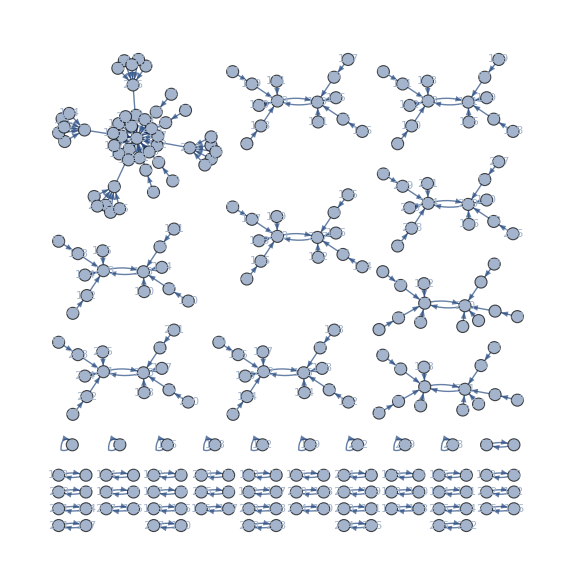

```mathematica
biggraph[graph_] :=
Module[{g=graph},
(*All 256 strategy pairs*)
inputlist = {};
Do[AppendTo[inputlist, Join[ConstantArray[0,8-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,255}];

bestresps = {};
Do[bestresps = AppendTo[bestresps,toBin[g[[i]][[2]],4]],{i,1,Length[g]}];

(*Find the best responses to the pairs*)
counterstrats = {};
Do[
p1 =FromDigits[inputlist[[i]][[1;;4]],2] + 1 ;
p2 = FromDigits[inputlist[[i]][[5;;8]],2] + 1 ;
AppendTo[counterstrats,Join[bestresps[[p2]],bestresps[[p1]]]];
,{i,1,256}];

(*Make the large graph*)
edges = {};
Do[AppendTo[edges, FromDigits[inputlist[[i]],2]->FromDigits[counterstrats[[i]],2]],{i,1,256}];
GraphPlot[edges, DirectedEdges->True, ImageSize->Large,VertexLabels->Placed[Automatic,Center],VertexSize->1.5,PlotStyle->Thick]
];
title = biggraph[edgeslist[[12]]]
(*Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/title.png",title]*)
```

```mathematica
complement[x_,l_]:=toBin[x[[1]]-1,8]==={
Boole[toBin[x[[l]]-1,8][[5]]==0],
Boole[toBin[x[[l]]-1,8][[7]]==0],
Boole[toBin[x[[l]]-1,8][[6]]==0],
Boole[toBin[x[[l]]-1,8][[8]]==0],
Boole[toBin[x[[l]]-1,8][[1]]==0],
Boole[toBin[x[[l]]-1,8][[3]]==0],
Boole[toBin[x[[l]]-1,8][[2]]==0],
Boole[toBin[x[[l]]-1,8][[4]]==0]}

P= markov[edgeslist[[4]]];
distr= P[256][[2]][[1]];
recclasses = MarkovProcessProperties[P,"RecurrentClasses"];
testtable = Table[complement[recclasses[[i]],Length[recclasses[[i]]]],{i,1,Length[recclasses]}];
Flatten[Position[testtable,False]]
recclasses[[Flatten[Position[testtable,False]]]]-1

comppercent = {};
Do[
P= markov[edgeslist[[i]]];
distr= P[256][[2]][[1]];
recclasses = MarkovProcessProperties[P,"RecurrentClasses"];
AppendTo[comppercent,Total[Table[Boole[complement[recclasses[[i]],Length[recclasses[[i]]]]],{i,1,Length[recclasses]}]]/Length[recclasses]];
,{i,1,Length[Graphs]}]

comppercents = {comppercent, 1 - comppercent}
comparea[delta_,type_]:=Sum[comppercents[[type]][[i]]*Area[ImplicitRegion[todraw[[i]]/.{d->delta,inside[[1]]->x,inside[[2]]->y},{x,y}]],{i,1,Length[todraw]}]
totalarea = comparea[1/2,1]+comparea[1/2,2]

(*plot = Plot[{comparea[d,1]/totalarea,comparea[d,2]/totalarea},{d,0,1},PlotLegends->{"Colluding","Noncolluding"},PlotRange->{0,1},AxesLabel->{"δ","Colluding probability"}]*)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28}

{{0},{1,16},{15,240},{9,144},{8,128},{11,208},{13,176},{17},{31,241},{25,145},{24,129},{27,209},{29,177},{255},{159,249},{143,248},{223,251},{191,253},{153},{137,152},{155,217},{157,185},{136},{139,216},{141,184},{187,221},{189},{219}}

{{0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1}}

1/2